```mathematica
(*data set "main" consists of the recorded experimental values,{frequency,position}*)
```

```mathematica
main= {{40.2,26.45},{40.5,28.10},{40.8,31.88},{41.1,27.05},{41.4, 26.18},{40.7,33.1},{40.73,33.58},{40.67,32.1},{40.55,28.8},{40.60,29.82},{40.85,30.3},{40.9,29.1},{41.6,25.9},{41.9,25.68},{38.5,25.38},{39.75,25.8},{36.5,25.2},{44.7,25.2}};
```

```mathematica
(*"zerpos" in the intial position of the laser light on the target apparatus, it is essentially the zero point of displacement; Note the semicolon suppresses output for this line*)
```

```mathematica
zeropos= 25;

(*the oscillator amplitude in millimeters; subtracting the zeropos gives the displacement*)
amplitude= main[[All,2]]-zeropos ;
```

```mathematica
frequency = main[[All,1]];
```

```mathematica
main1 = Table[{frequency[[i]], amplitude[[i]]},{i,1,Length[amplitude]}]
```

{{40.2,1.45},{40.5,3.1},{40.8,6.88},{41.1,2.05},{41.4,1.18},{40.7,8.1},{40.73,8.58},{40.67,7.1},{40.55,3.8},{40.6,4.82},{40.85,5.3},{40.9,4.1},{41.6,0.9},{41.9,0.68},{38.5,0.38},{39.75,0.8},{36.5,0.2},{44.7,0.2}}

```mathematica
amp= 9; (*amplitude*)

freq0= 40.73;(*"freq0 " is the center frequency*)
```

```mathematica
qq=46.8; (*The oscillator Q-factor; changes this affect how much the graph fits into the par*)

main1=Table[{x,((amp*freq0)/(2*qq))/Sqrt[((x-freq0)^2+((freq0/(2*qq))^2))]+0.1*RandomVariate[NormalDistribution[]]},{x,35,45,0.5}]
```

{{35.,0.664762},{35.5,0.896528},{36.,0.762188},{36.5,1.03494},{37.,1.03409},{37.5,1.194},{38.,1.36867},{38.5,1.75496},{39.,2.35199},{39.5,3.04405},{40.,4.58304},{40.5,8.09144},{41.,7.62763},{41.5,4.42327},{42.,2.92503},{42.5,2.16812},{43.,1.65646},{43.5,1.57303},{44.,1.18782},{44.5,1.17566},{45.,0.987487}}

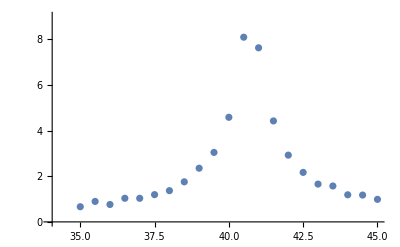

```mathematica
ListPlot[main1,PlotRange->{{34,45},{0,9}}]
```

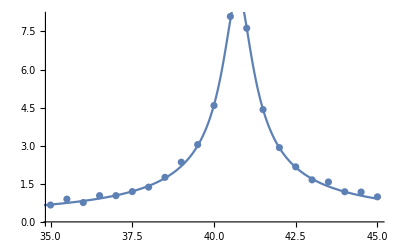

```mathematica
amp =9;
freq0=40.73;
qq=46.8;

Show[ListPlot[main1],Plot[((amp*freq0)/(2*qq))/Sqrt[((x-freq0)^2+((freq0/(2*qq))^2))],{x,34,45},PlotRange->All]]
```

```mathematica
(*Change the declaration of the frequency, amplitude and Q-factor to a different name; mathematica will run into problems otherwise: amp->am1, freq0->fre01, qq->qq1. Make sure the new declaration are highted in blue otherwise it wont work.*)

fit =NonlinearModelFit[main1,((am1*freq01)/(2*qq1))/(Sqrt[((x-fre01)^2+((fre01/(2*qq1))^2))]),{{am1,9},{qq1,46.8},{fre01,40.73}},x]
```

FittedModel[3.97213/(√(0.193467+(-«18»+x)^2))]

```mathematica
fit[{"BestFit","ParameterTable"}]
```

{3.97213/(√(0.193467+(-40.7229+x)^2)), | Estimate | Standard Error | t-Statistic | P-Value
am1 | 9.02912 | 0.0970738 | 93.0129 | 1.33116×10^-25
qq1 | 46.292 | 0.857477 | 53.9863 | 2.30016×10^-21
fre01 | 40.7229 | 0.00628254 | 6481.92 | 9.01696×10^-59}

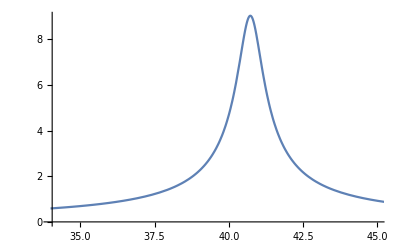

```mathematica
Show[ListPlot[main,PlotRange->{{34,45},{0,9}}],Plot[fit[x],{x,34,46}]]
```